```mathematica
<<life`;
bool[True]//loob
```

True

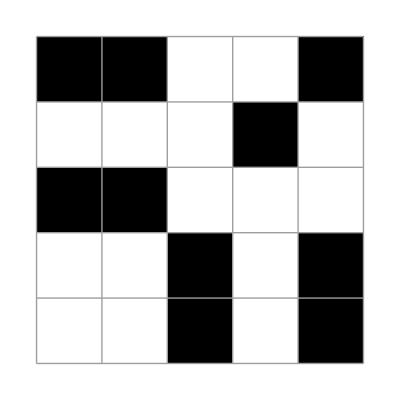
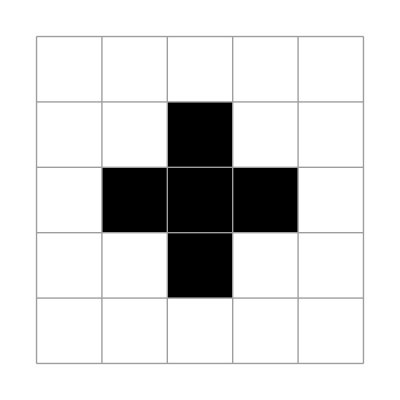

```mathematica
Clear[update,xp];
<<life`;
count[k_,{i_,j_}]:=BooleanCountingFunction[{k},Delete[Flatten[Array[x,{3,3},{i,j}-1]],5]];
xpArray2=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
update[xpArray_]:=Module[
{formulaIJ,formula,varlist,out1}

,x[_,0]=False;x[0,_]=False;


	x[_,6]=False;
	x[6,_]=False;
({{xp[1,1], xp[1,2], xp[1,3], xp[1,4], xp[1,5]}, {xp[2,1], xp[2,2], xp[2,3], xp[2,4], xp[2,5]}, {xp[3,1], xp[3,2], xp[3,3], xp[3,4], xp[3,5]}, {xp[4,1], xp[4,2], xp[4,3], xp[4,4], xp[4,5]}, {xp[5,1], xp[5,2], xp[5,3], xp[5,4], xp[5,5]}})=loob[xpArray];
formulaIJ=(and@{Nothing,(x[##]&&count[{0},{##}])~Implies~!xp[##],(x[##]&&count[{1},{##}])~Implies~!xp[##],(x[##]&&count[{2},{##}])~Implies~xp[##],(x[##]&&count[{3},{##}])~Implies~xp[##],(x[##]&&count[{4},{##}])~Implies~!xp[##],(x[##]&&count[{5},{##}])~Implies~!xp[##],(x[##]&&count[{6},{##}])~Implies~!xp[##],(x[##]&&count[{7},{##}])~Implies~!xp[##],(x[##]&&count[{8},{##}])~Implies~!xp[##]
(*not*),(!x[##]&&count[{0},{##}])~Implies~!xp[##],(!x[##]&&count[{1},{##}])~Implies~!xp[##],(!x[##]&&count[{2},{##}])~Implies~!xp[##],(!x[##]&&count[{3},{##}])~Implies~xp[##],(!x[##]&&count[{4},{##}])~Implies~!xp[##],(!x[##]&&count[{5},{##}])~Implies~!xp[##],(!x[##]&&count[{6},{##}])~Implies~!xp[##],(!x[##]&&count[{7},{##}])~Implies~!xp[##],(!x[##]&&count[{8},{##}])~Implies~!xp[##]})&;
formula=and@Flatten@Array[formulaIJ,{5,5}];
varlist=Flatten@Array[x,{5,5}];
asdf=SatisfiabilityInstances[formula,varlist];
If[Length[asdf]==0,
"unsatisfiable",
out1=Array[x,{5,5}]/.Thread[varlist->RandomChoice[asdf]];
bool@out1
]

];
(*X0=update[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 0, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]//update;*)
(*X0=FixedPointList[update,({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 0, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})];*)
xPArray=({{0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}});
output=NestWhileList[update,xPArray,!StringQ[#]&];
X0=output[[-2]];

plt/@NestList[updateLife2[{5,5}][ #]&,
X0,Length[output]-2]
```

```mathematica
lr
```

plt::shdw: Symbol plt appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

and::shdw: Symbol and appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

loob::shdw: Symbol loob appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

bool::shdw: Symbol bool appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
lr
```

lifePlot::shdw: Symbol lifePlot appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

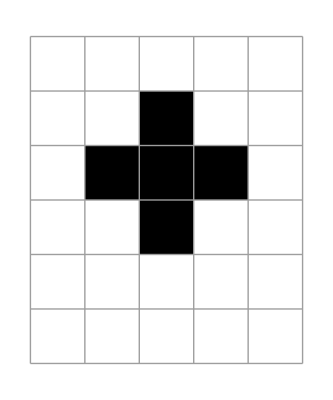
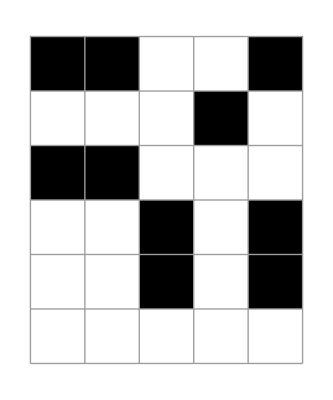
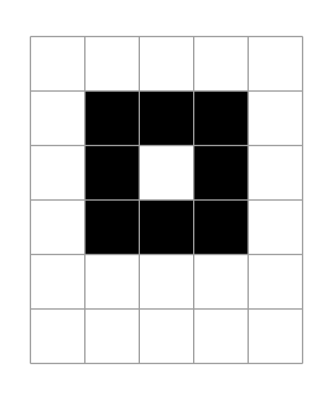
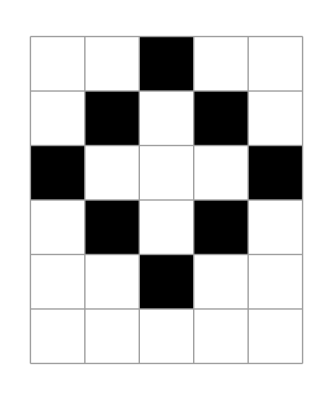
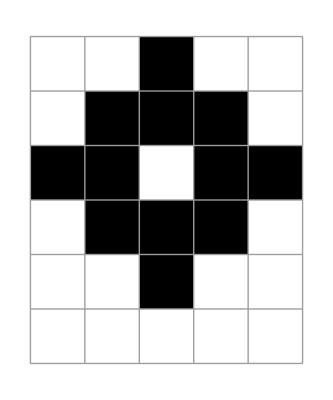
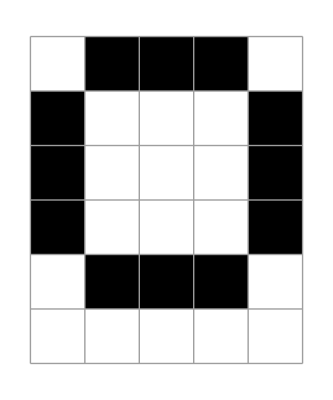
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/00_still_life_stack_question/001_counting_function/countModule.m"];
xPArray=({{0, 0, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPArray]*)
{xPArray//plt,rollBackPlot[xPArray]}
```

```mathematica
AAAAA
```

```mathematica
Clear[xp];
Evaluate[Array[xp,{5,5}]]=loob[xPArray]
```

{{False,False,False,False,False},{False,False,True,False,False},{False,True,True,True,False},{False,False,True,False,False},{False,False,False,False,False}}

```mathematica
life44
```

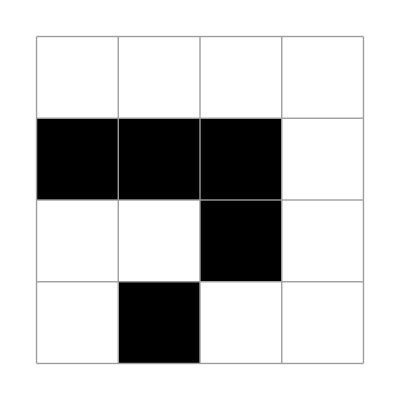
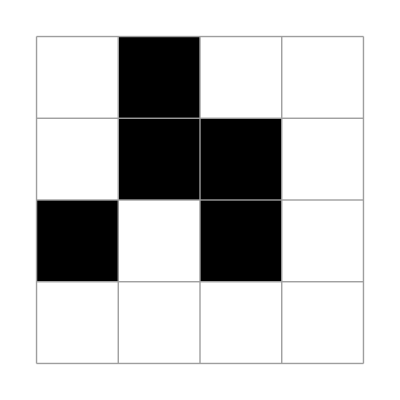
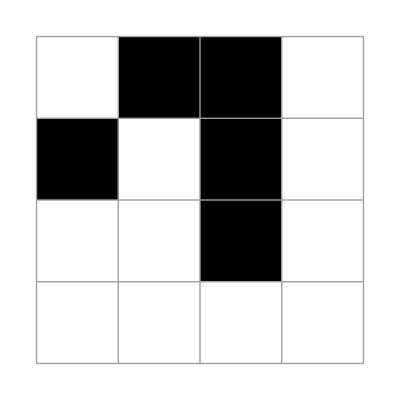
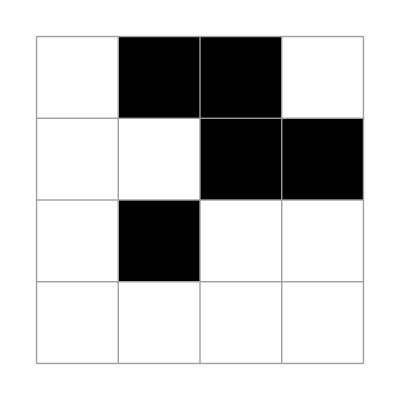

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```